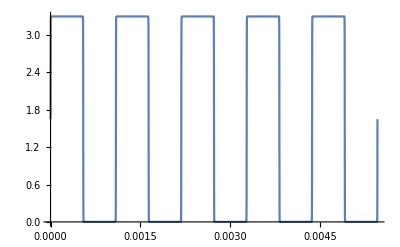

NDSolve::structurallysingular: The dummy derivative method found the differential algebraic equation to be structurally singular.

NDSolve::irfail: Unable to reduce the index of the system to 0 or 1.

NDSolve[{iUz[t]==iR1[t],iR1[t]+iR2[t]==iC1[t],iR3[t]==iC2[t]+iR3[t],1.65 (1+Tanh[100 Sin[1834 π t]])==u1[t],u1[t]-u2[t]==10000 iR2[t],-u2[t]+u3[t]==10000 iR2[t],-u3[t]==R3 iR3[t],(33 u2'[t])/1000000000==iC1[t],C2 u3'[t]==iC2[t],u2[0]==0,u2[0]==0},{u1[t],u2[t],u3[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],iUz[t]},{t,0,5/917},StartingStepSize→1/1000000000,Method→{IndexReduction→True}]

NDSolve::dsvar: 1.11388×10^-7 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{iUz[1.11388×10^-7]==iR1[1.11388×10^-7],iR1[1.11388×10^-7]+iR2[1.11388×10^-7]==iC1[1.11388×10^-7],iR3[1.11388×10^-7]==iC2[1.11388×10^-7]+iR3[1.11388×10^-7],1.75575==u1[1.11388×10^-7],«3»,(33 u2'[1.11388×10^-7])/1000000000==iC1[1.11388×10^-7],C2 u3'[1.11388×10^-7]==iC2[1.11388×10^-7],u2[0]==0,«1»},«3»,Method→{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.11388×10^-7 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{iUz[1.11388×10^-7]==iR1[1.11388×10^-7],iR1[1.11388×10^-7]+iR2[1.11388×10^-7]==iC1[1.11388×10^-7],iR3[1.11388×10^-7]==iC2[1.11388×10^-7]+iR3[1.11388×10^-7],1.75575==u1[1.11388×10^-7],«3»,3.3×10^-8 u2'[1.11388×10^-7]==iC1[1.11388×10^-7],C2 u3'[1.11388×10^-7]==iC2[1.11388×10^-7],u2[0.]==0.,«1»},«3»,Method→{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000111388 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{iUz[0.000111388]==iR1[0.000111388],iR1[0.000111388]+iR2[0.000111388]==iC1[0.000111388],iR3[0.000111388]==iC2[0.000111388]+iR3[0.000111388],3.3==u1[0.000111388],«3»,(33 u2'[0.000111388])/1000000000==iC1[0.000111388],C2 u3'[0.000111388]==iC2[0.000111388],u2[0]==0,«1»},«3»,Method→{…→«4»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

-Graphics-

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

```mathematica
ClearAll("Global`*");

rovnice = { 
iUz[t]== iR1[t],
iR1[t] + iR2[t] == iC1[t],
iR3[t] == iR3[t]+iC2[t],
uZ[t]==u1[t],
u1[t]-u2[t]==R1*iR2[t],
u3[t] - u2[t] == R2 * iR2[t],
-u3[t] == R3*iR3[t],
C1*u2'[t]== iC1[t],
C2*u3'[t]==iC2[t],
u2[0]==0,
u2[0]==0 
};

nezname = {
u1[t], u2[t], u3[t],
iR1[t], iR2[t], iR3[t],
iC1[t], iC2[t],
iUz[t]
};

soucastky = {
R1-> 10*10^3, R2 -> 10*10^3, R2 -> 10*10^6,
C1 -> 33*10^-9, C1 -> 22*10^-9 
};

amplituda = 3.3;
frekvence = 917;
perioda = 1/frekvence;
tmax = 5 * perioda;

uZ[t_] := amplituda*(1+Tanh[100*Sin[2*π*frekvence*t]])/2;

Plot[uZ[t], {t,0,tmax}]


reseni = NDSolve[rovnice /. soucastky, nezname,{t, 0, tmax}, StartingStepSize->10^-9, Method->{"IndexReduction" -> True}]

Plot[{u1[t] /. reseni, u2[t] /. reseni, u3[t] /. reseni}, {t, 0, tmax}]
```

```mathematica
(*priklad 1.1*)
ClearAll["Global`*"]

uf1=12+7*ⅉ (* [v] *)
amplituda = Abs[uf1]
φ=Arg[uf1]
```

12+7 ⅈ

√193

ArcTan[7/12]

```mathematica
(*priklad 1.2*)
ClearAll["Global`*"]
if1 = 14+8ⅉ
amplituda = Abs[if1]
faze = Arg[if1]
```

14+8 ⅈ

2 √65

ArcTan[4/7]

```mathematica
(*priklad 2.1*)
ClearAll["Global`*"]
amplituda = 15
φ = π/3
fazor = amplituda*ⅇ^(ⅉ*φ)
```

15

π/3

15 ⅇ^((ⅈ π)/3)

```mathematica
(*priklad 2.2*)
ClearAll["Global`*"]
amplituda = 4.8
φ = 1.2
fazor = amplituda*ⅇ^(ⅉ*φ)
```

4.8

1.2

1.73932+4.47379 ⅈ

-6.78402+6.21426 ⅈ

100

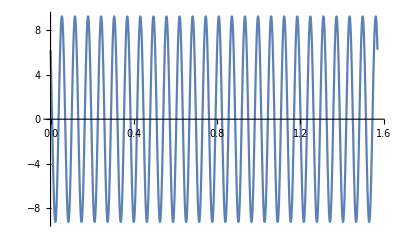

```mathematica
(*priklad 3.1*)
ClearAll["Global`*"]
u3=9.2* ⅇ^(ⅈ*2.4)
ω =100
Plot[Im[u3*ⅇ^(ⅈ*ω*t)], {t, 0, π/2}]
```

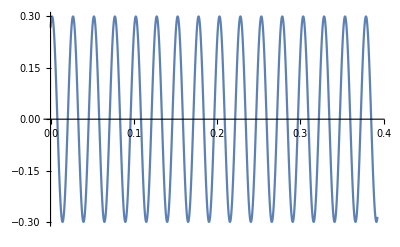

0.136079+0.267362 ⅈ

250

-Graphics-

```mathematica
(*priklad 3.2*)
ClearAll["Global`*"]
i[t_] := 0.3 * Sin[250*t+1.1]
Plot[i[t], {t,0,π/8}]

iff= 0.3*ⅇ^(ⅉ*1.1)
ω = 250
Plot[Im[iff*ⅇ^(ⅉ*ω*t)], {t, 0, π/8}]
(*stejny vysledek*)
```

12.8+5.2 ⅈ

200

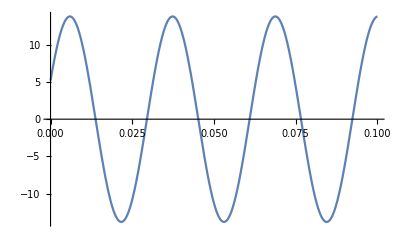

```mathematica
(*priklad 4.1*)
ClearAll["Global`*"]
i4 = 12.8 + 5.2 * ⅉ
ω = 200
Plot[Im[i4*ⅇ^(ⅉ*ω*t)], {t,0,0.1}]
```

3.2+3.7 ⅈ

153

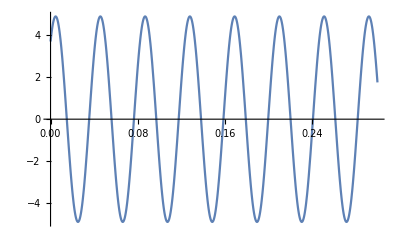

```mathematica
(*priklad 4.2*)
ClearAll["Global`*"]
i4 = 3.2 + 3.7* ⅉ
ω = 153
Plot[Im[i4*ⅇ^(ⅉ*ω*t)], {t,0,0.3}]
```

```mathematica
(*priklad 5*)
```

{iUz[t]==iR1[t],iR1[t]==iC1[t]+iR2[t],uZ[t]==u1[t],u1[t]-u2[t]==R1 iR1[t],u2[t]==R2 iR2[t],C1 u2'[t]==iC1[t],u2[0]==0}

{iUz[t],u1[t],u2[t],iR1[t],iR2[t],iC1[t]}

{R1→10000,R2→10000,C1→1/100000000}

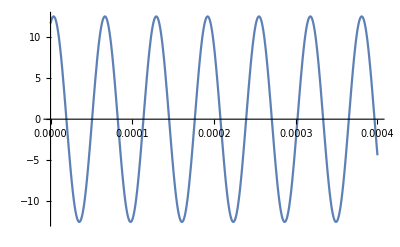

{{iUz[t]→InterpolatingFunction[…][t],u1[t]→InterpolatingFunction[…][t],u2[t]→InterpolatingFunction[…][t],iR1[t]→InterpolatingFunction[…][t],iR2[t]→InterpolatingFunction[…][t],iC1[t]→InterpolatingFunction[…][t]}}

```mathematica
ClearAll["Global`*"]
rovnice= {
iUz[t]==iR1[t],
iR1[t] == iC1[t] + iR2[t],
uZ[t] == u1[t],
u1[t]-u2[t]== R1*iR1[t],
u2[t] ==R2*iR2[t],
C1*u2'[t] == iC1[t],
u2[0]==0
}

nezname = {
iUz[t], 
u1[t], u2[t],
iR1[t], iR2[t],
iC1[t]
}

soucastky = {
R1->10*10^3, R2->10*10^3, C1->10*10^-9
}

amplituda = 12.5;
φ = 1.2;
omega = ω->10^5;
tmax = 0.4*10^-3;

uZ[t_] := amplituda*Sin[ω*t+ φ] /. omega

Plot[uZ[t], {t,0,tmax}]

reseni = NDSolve[rovnice /. soucastky, nezname, {t, 0, tmax}]
```